```mathematica
<<VisualDebug`
VisualDebug[2+2]
```

VisualDebug[2+2]

```mathematica
expr=Hold[{2+3,5^2,9+0}];
stringExpr=FullForm[expr]//ToString;
length=StringLength[stringExpr];
Manipulate[
startString=StringTake[stringExpr,{1,startPos-1}];
midString=StringTake[stringExpr,{startPos, endPos}];
endString=StringTake[stringExpr,{endPos+1,length}];
Row[{startString,Style[midString,FontColor->ColorData["Rainbow"][0.5]],endString}];
Row[{Style[Extract[expr,mainPart,HoldForm],FontColor->ColorData["Rainbow"][0.5]]}],

{startPos,1,endPos,1,Appearance->"Labeled"},
{{endPos,length},startPos, length,1,Appearance->"Labeled"},
{mainPart,0, Length[expr],1}
]
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 0}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {1, 47}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[stringExpr, {48, length}].

General::stop: Further output of StringTake :: strse will be suppressed during this calculation.

Extract::partd: Part specification {1} is longer than depth of object.

```mathematica
StringLength["Abc"]
```

3

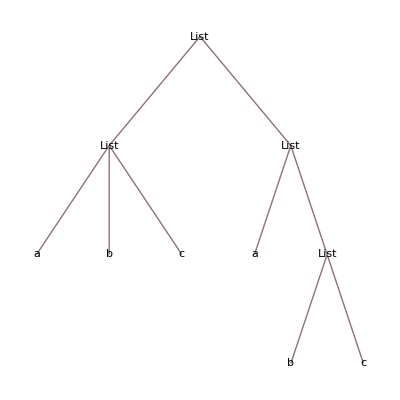

```mathematica
{{a,b,c},{a,{b,c}}}//TreeForm
```

```mathematica
a->0
{a}->1
{a,b}->{2,{0,0}}
shape@{{a,d},{b,c}}
```

a→0

{a}→1

{a,b}→{2,{0,0}}

shape[{{a,d},{b,c}}]

```mathematica
Depth[HoldForm[a]]
```

2

```mathematica
Remove[shape]
SetAttributes[shape,HoldAll]
shape[expr_]:=Module[
{

},
If[Depth[Unevaluated[expr]]==1,
Return[0],
Return[{Length[Unevaluated[expr]],shape@@@(Map[Unevaluated,ReplacePart[Hold[expr],{1,0}->List],{2}]//ReleaseHold)}]
]
]
```

```mathematica
expr1=Hold[2+2+Integrate[x^6+3,{x,0,2}]]
sh=shape[2+2+Integrate[x^6+3,{x,0,2}]]
Position[%,_List]
Extract[expr1,{1,3,1,1,2}]
```

Hold[2+2+∫_0^2 (x^6+3)ⅆx]

{3,{0,0,{2,{{2,{{2,{0,0}},0}},{3,{0,0,0}}}}}}

{{2,3,2,1,2,1,2},{2,3,2,1,2,1},{2,3,2,1,2},{2,3,2,1},{2,3,2,2,2},{2,3,2,2},{2,3,2},{2,3},{2},{}}

6

```mathematica
Extract[expr1,{1,3,1},Hold]
```

Hold[x^6+3]

```mathematica
Position[expr1,_]//Sort[#,Length[#1]<Length[#2]&]&
```

{{},{1},{0},{1,3},{1,2},{1,1},{1,0},{1,3,2},{1,3,1},{1,3,0},{1,3,2,3},{1,3,2,2},{1,3,2,1},{1,3,2,0},{1,3,1,2},{1,3,1,1},{1,3,1,0},{1,3,1,1,2},{1,3,1,1,1},{1,3,1,1,0}}

```mathematica
Position[expr1,_,Heads->False]//Sort//Rest
```

{{1},{1,1},{1,2},{1,3},{1,3,1},{1,3,2},{1,3,1,1},{1,3,1,2},{1,3,2,1},{1,3,2,2},{1,3,2,3},{1,3,1,1,1},{1,3,1,1,2}}

```mathematica
Position[expr1,_,Heads->True]//Sort//Rest
```

{{0},{1},{1,0},{1,1},{1,2},{1,3},{1,3,0},{1,3,1},{1,3,2},{1,3,1,0},{1,3,1,1},{1,3,1,2},{1,3,2,0},{1,3,2,1},{1,3,2,2},{1,3,2,3},{1,3,1,1,0},{1,3,1,1,1},{1,3,1,1,2}}

```mathematica
Remove[a]
```

```mathematica
a/:a+b=Exp
```

Exp

```mathematica
allowedParts=Position[expr1,_,Heads->False]//Sort//Rest
```

{{1},{1,1},{1,2},{1,3},{1,3,1},{1,3,2},{1,3,1,1},{1,3,1,2},{1,3,2,1},{1,3,2,2},{1,3,2,3},{1,3,1,1,1},{1,3,1,1,2}}

```mathematica
Remove[debug]
```

```mathematica
expr1=Hold[2+2+Integrate[x^6+3,{x,0,2}]];
SetAttributes[debug,HoldFirst]
debug[origExpr_,opts:OptionsPattern[{"Heads"->False}]]:=Module[
{
currentExpr,allowedParts,part
},
currentExpr=origExpr;
allowedParts=Position[currentExpr,_,Heads->OptionValue["Heads"]]//Sort//Rest;
Manipulate[
part=allowedParts[[partNumber]];
ReplacePart[currentExpr,part->Style[Extract[currentExpr,part,HoldForm],FontColor->RGBColor[1,0,0],Bold]],

{partNumber,If[OptionValue["Heads"],2,1],Dynamic[Length[allowedParts]],1},
Row[{
Button["Evaluate",
currentExpr=ReplacePart[currentExpr,part->Evaluate[Extract[currentExpr,part]]];
allowedParts=Position[currentExpr,_,Heads->OptionValue["Heads"]]//Sort//Rest
],
Button["Reset",
partNumber=If[OptionValue["Heads"],2,1];
currentExpr=origExpr;
allowedParts=Position[currentExpr,_,Heads->OptionValue["Heads"]]//Sort//Rest
]
}]
]
]
debug[expr1,Heads->False]
```

Part::partd: Part specification allowedParts$1308932 ⟦ 1 ⟧ is longer than depth of object.

Extract::psl: Position specification allowedParts$1308932 ⟦ 1 ⟧ in Extract[currentExpr$1308932, allowedParts$1308932 ⟦ 1 ⟧, HoldForm] is not a machine-sized integer or a list of machine-sized integers.

Part::partd: Part specification allowedParts$1308932 ⟦ 1 ⟧ is longer than depth of object.

Extract::psl: Position specification allowedParts$1308932 ⟦ 1 ⟧ in Extract[currentExpr$1308932, allowedParts$1308932 ⟦ 1 ⟧, HoldForm] is not a machine-sized integer or a list of machine-sized integers.

Part::partd: Part specification allowedParts$1308932 ⟦ 1 ⟧ is longer than depth of object.

Extract::psl: Position specification allowedParts$1308932 ⟦ 1 ⟧ in Extract[currentExpr$1308932, allowedParts$1308932 ⟦ 1 ⟧, HoldForm] is not a machine-sized integer or a list of machine-sized integers.

Part::partd: Part specification allowedParts$1308932 ⟦ 1 ⟧ is longer than depth of object.

Extract::psl: Position specification allowedParts$1308932 ⟦ 1 ⟧ in Extract[currentExpr$1308932, allowedParts$1308932 ⟦ 1 ⟧, HoldForm] is not a machine-sized integer or a list of machine-sized integers.

Part::partd: Part specification allowedParts$1308932 ⟦ 1 ⟧ is longer than depth of object.

Extract::psl: Position specification allowedParts$1308932 ⟦ 1 ⟧ in Extract[currentExpr$1308932, allowedParts$1308932 ⟦ 1 ⟧, HoldForm] is not a machine-sized integer or a list of machine-sized integers.

## From SE

```mathematica
SetAttributes[step,HoldAll]
step[expr_]:=Module[{P},P=(P= Return[#/.HoldForm[x_]:>Defer[step[x]],TraceScan]&)&;
TraceScan[P,expr,TraceDepth->1]]
```

```mathematica
expr1
step[2+2+∫_0^2 (x^6+3)ⅆx]
```

Hold[2+2+∫_0^2 (x^6+3)ⅆx]

step[2+2+170/7]

```mathematica
step[2+2+170/7]
```

step[2+2+170/7]

```mathematica
step[2+2+170/7]
```

step[2+2+170/7]

```mathematica
Hold[2+3^3^7]//FullForm
```

Hold[Plus[2,Power[3,Power[3,7]]]]

```mathematica
ClearAll[watch]
SetAttributes[watch,HoldAllComplete]
watch[expr_,fn_: Print]:=Module[{enter,exit,depth=0},SetAttributes[{enter,exit},HoldAllComplete];enter[args__]:=With[{d=depth++},fn[Hold["enter",d,args]]];exit[args__]:=With[{d=--depth},fn[Hold["exit",d,args]]];TraceScan[enter,expr,_,exit]]
```

```mathematica
?TraceScan
```

TraceScan[f,expr] applies f to all expressions used in the evaluation of expr. 
TraceScan[f,expr,form] includes only those expressions which match form. 
TraceScan[f,expr,s] includes all evaluations which use transformation rules associated with the symbol s. 
TraceScan[f,expr,form,fp] applies f before evaluation and fp after evaluation to expressions used in the evaluation of expr.

```mathematica
?TracePrint
```

TracePrint[expr] prints all expressions used in the evaluation of expr. 
TracePrint[expr,form] includes only those expressions which match form. 
TracePrint[expr,s] includes all evaluations which use transformation rules associated with the symbol s.

```mathematica
?Trace
```

RowBox[{"Trace", "[", StyleBox["expr", "TI"], "]"}] generates a list of all expressions used in the evaluation of StyleBox["expr", "TI"]. 
RowBox[{"Trace", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"]}], "]"}] includes only those expressions which match StyleBox["form", "TI"]. 
RowBox[{"Trace", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["s", "TI"]}], "]"}] includes all evaluations which use transformation rules associated with the symbol StyleBox["s", "TI"].

## My step function

```mathematica
Remove[step]
<<VisualDebug`
```

```mathematica
s[x_]:=Exp[x]
f[x_]:=k[x]
k[x_]:=x-2
g[x_]:=Sin[x]
h[x_]:=x^2
```

```mathematica
step[s[f[g[h[4]]]]]
step[s[f[g[16]]]]
step[s[f[Sin[16]]]]
step[s[k[Sin[16]]]]
```

s[f[g[16]]]

s[f[Sin[16]]]

s[k[Sin[16]]]

s[-2+Sin[16]]

```mathematica
expr=Unevaluated[2+3^4]
stepTrace[2+3^4]
```

83

{2+3^4,2+81,83}

```mathematica
k=2
Head[Unevaluated[k]]
```

2

Symbol

```mathematica
stepTrace[s[f[g[h[4]]]]]
```

{s[f[g[h[4]]]],s[f[g[16]]],s[f[Sin[16]]],s[k[Sin[16]]],s[-2+Sin[16]],ⅇ^(-2+Sin[16])}

## A step test

```mathematica
<<VisualDebug`
Integrate[x+x,{x,0,1}]
```

1

```mathematica
step[Integrate[x+x, {x, 0, 1}]]
step[Integrate[2x, {x, 0, 1}]]
```

∫_0^1 2 xⅆx

1

```mathematica
stepTrace[Integrate[x+x, {x, 0, 1}]]
```

{∫_0^1 (x+x)ⅆx,∫_0^1 2 xⅆx,1}